### Start choosing the example:

```mathematica
t=11;
beta = 0;
A = 0.2;
g[x]
```

g[x]

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];
Cost[j_,1->2]:=If[j!=0, 45,0];
Cost[j_,3->4]:= If[j!=0,45,0];
Cost[j_,1->3]:=If[j!=0, Abs[j]/100,0];
Cost[j_,2->4]:= If[j!=0,Abs[j]/100,0];
Cost[j_,2->3]:= If[j!=0,0,0];
Data=<|"Vertices List"->{1,2,3,4},"Adjacency Matrix"->{{0,1,1,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{4,U1}},"Switching Costs"->{(*{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6},{1,3,4,S7},{4,3,1,S8},{1,3,2,S9},{2,3,1,S10},{3,4,2,S11},{2,4,3,S12},{2,3,4,S13},{4,3,2,S14},{3,1,2,S15},{2,1,3,S16}*)}|>;
(crit=CriticalCongestionSolver[d2e=Data2Equations[Data/.{I1->4000,U1->0, S1->1,S2->1,S3->1,S4->1,S5->1,S6->1, S7->1,S8->1,S9->1,S10->0,S11->0,S12->0,S13->1,S14->1,S15->0,S16->0}]];)//AbsoluteTiming
```

Iterative boolean convert took 0.015939 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

{0.297916,Null}

```mathematica
IsNonLinearSolution[crit][crit["AssoCritical"]]
```

All restrictions are True

Nrhs: {1955.,1980.,0.,1980.,1955.}
{-j1+j2-If[-j1+j2≠0,45,0],-j3+j4-If[-j3+j4≠0,1/100 Abs[-j3+j4],0],-j5+j6-If[-j5+j6≠0,0,0],-j7+j8-If[-j7+j8≠0,1/100 Abs[-j7+j8],0],j10-j9-If[j10-j9≠0,45,0]}

Nlhs: {0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9}

Max error for non-linear solution: 1980.

<|u1→4000.,u2→2000.,u3→4000.,u4→2000.,u5→2000.,u6→2000.,u7→2000.,u8→0.,u9→2000.,u10→0.,u11→0.,u12→0.,u13→4000.,u14→4000.,j1→0.,j2→2000.,j3→0.,j4→2000.,j5→0.,j6→0.,j7→0.,j8→2000.,j9→0.,j10→2000.,j11→0.,j12→4000.,j13→0.,j14→4000.,jt1→0.,jt2→0.,jt3→0.,jt4→0.,jt5→2000.,jt6→2000.,jt7→0.,jt8→2000.,jt9→0.,jt10→0.,jt11→0.,jt12→0.,jt13→0.,jt14→2000.,jt15→0.,jt16→0.,jt17→0.,jt18→0.,jt19→0.,jt20→2000.,jt21→0.,jt22→2000.,jt23→0.,jt24→0.|>

```mathematica
(nn=NonLinear[crit];)//AbsoluteTiming
nn["AssoNonCritical"]
```

Iterative boolean convert took 0.389841 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 12.5

Iterative boolean convert took 0.49773 seconds to terminate

Iterative boolean convert took 0.024343 seconds to terminate

Iterative boolean convert took 0.022057 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 12.4688

Iterative boolean convert took 0.427226 seconds to terminate

Iterative boolean convert took 0.023024 seconds to terminate

Iterative boolean convert took 0.026489 seconds to terminate

Iterative boolean convert took 0.00002 seconds to terminate

Max error for non-linear solution: 12.4376

Iterative boolean convert took 0.400425 seconds to terminate

Iterative boolean convert took 0.024956 seconds to terminate

Iterative boolean convert took 0.02762 seconds to terminate

Iterative boolean convert took 0.000021 seconds to terminate

Max error for non-linear solution: 12.4065

Iterative boolean convert took 0.395509 seconds to terminate

Iterative boolean convert took 0.055143 seconds to terminate

Iterative boolean convert took 0.076717 seconds to terminate

Iterative boolean convert took 0.000023 seconds to terminate

Max error for non-linear solution: 12.3755

Iterative boolean convert took 0.432107 seconds to terminate

Iterative boolean convert took 0.027123 seconds to terminate

Iterative boolean convert took 0.024893 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 12.3445

Iterative boolean convert took 0.453872 seconds to terminate

Iterative boolean convert took 0.054596 seconds to terminate

Iterative boolean convert took 0.07676 seconds to terminate

Iterative boolean convert took 0.000028 seconds to terminate

Max error for non-linear solution: 12.3137

Iterative boolean convert took 0.400623 seconds to terminate

Iterative boolean convert took 0.073211 seconds to terminate

Iterative boolean convert took 0.072192 seconds to terminate

Iterative boolean convert took 0.000025 seconds to terminate

Max error for non-linear solution: 12.2829

Iterative boolean convert took 0.418072 seconds to terminate

Iterative boolean convert took 0.088924 seconds to terminate

Iterative boolean convert took 0.07119 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 12.2522

Iterative boolean convert took 0.404995 seconds to terminate

Iterative boolean convert took 0.052064 seconds to terminate

Iterative boolean convert took 0.0854 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 12.2215

Iterative boolean convert took 0.409547 seconds to terminate

Iterative boolean convert took 0.062168 seconds to terminate

Iterative boolean convert took 0.086704 seconds to terminate

Iterative boolean convert took 0.00004 seconds to terminate

Max error for non-linear solution: 12.191

Iterative boolean convert took 0.418359 seconds to terminate

Iterative boolean convert took 0.026422 seconds to terminate

Iterative boolean convert took 0.025431 seconds to terminate

Iterative boolean convert took 0.00002 seconds to terminate

Max error for non-linear solution: 12.1605

Iterative boolean convert took 0.411486 seconds to terminate

Iterative boolean convert took 0.054056 seconds to terminate

Iterative boolean convert took 0.090305 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 12.1301

Iterative boolean convert took 0.445891 seconds to terminate

Iterative boolean convert took 0.058211 seconds to terminate

Iterative boolean convert took 0.062264 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 12.0998

Iterative boolean convert took 0.384501 seconds to terminate

Iterative boolean convert took 0.040488 seconds to terminate

Iterative boolean convert took 0.030783 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 12.0695

Iterated 15 times out of 15

{13.7082,Null}

<|u1→82326153081/1250000000,u2→134478459243/5000000000,u3→82326153081/1250000000,u4→194826153081/5000000000,u5→134478459243/5000000000,u6→194826153081/5000000000,u7→134478459243/5000000000,u8→0,u9→194826153081/5000000000,u10→0,u11→0,u12→0,u13→82326153081/1250000000,u14→82326153081/1250000000,j1→0,j2→19078729841331/10000000000,j3→0,j4→20921270158669/10000000000,j5→921270158669/5000000000,j6→0,j7→0,j8→20921270158669/10000000000,j9→0,j10→19078729841331/10000000000,j11→0,j12→4000,j13→0,j14→4000,jt1→0,jt2→0,jt3→0,jt4→0,jt5→19078729841331/10000000000,jt6→20921270158669/10000000000,jt7→0,jt8→19078729841331/10000000000,jt9→0,jt10→921270158669/5000000000,jt11→0,jt12→0,jt13→921270158669/5000000000,jt14→19078729841331/10000000000,jt15→0,jt16→0,jt17→0,jt18→0,jt19→0,jt20→20921270158669/10000000000,jt21→0,jt22→19078729841331/10000000000,jt23→0,jt24→0|>

```mathematica
nn2=NonLinear[nn];
nn2=NonLinear[nn2];
```

Iterative boolean convert took 0.463224 seconds to terminate

Iterative boolean convert took 0.039978 seconds to terminate

Iterative boolean convert took 0.082381 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 12.0394

Iterative boolean convert took 0.412789 seconds to terminate

Iterative boolean convert took 0.044601 seconds to terminate

Iterative boolean convert took 0.045023 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 12.0093

Iterative boolean convert took 0.604748 seconds to terminate

Iterative boolean convert took 0.062249 seconds to terminate

Iterative boolean convert took 0.081707 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 11.9792

Iterative boolean convert took 0.538603 seconds to terminate

Iterative boolean convert took 0.018425 seconds to terminate

Iterative boolean convert took 0.031087 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 11.9493

Iterative boolean convert took 0.41726 seconds to terminate

Iterative boolean convert took 0.044259 seconds to terminate

Iterative boolean convert took 0.102191 seconds to terminate

Iterative boolean convert took 0.000021 seconds to terminate

Max error for non-linear solution: 11.9194

Iterative boolean convert took 0.544304 seconds to terminate

Iterative boolean convert took 0.130005 seconds to terminate

Iterative boolean convert took 0.145237 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 11.8896

Iterative boolean convert took 0.918418 seconds to terminate

Iterative boolean convert took 0.115235 seconds to terminate

Iterative boolean convert took 0.146401 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 11.8599

Iterative boolean convert took 0.77462 seconds to terminate

Iterative boolean convert took 0.043103 seconds to terminate

Iterative boolean convert took 0.070282 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 11.8302

Iterative boolean convert took 0.506411 seconds to terminate

Iterative boolean convert took 0.105509 seconds to terminate

Iterative boolean convert took 0.08485 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 11.8007

Iterative boolean convert took 0.578016 seconds to terminate

Iterative boolean convert took 0.084393 seconds to terminate

Iterative boolean convert took 0.09002 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 11.7712

Iterative boolean convert took 0.446573 seconds to terminate

Iterative boolean convert took 0.061147 seconds to terminate

Iterative boolean convert took 0.091002 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 11.7417

Iterative boolean convert took 0.504699 seconds to terminate

Iterative boolean convert took 0.068636 seconds to terminate

Iterative boolean convert took 0.067531 seconds to terminate

Iterative boolean convert took 0.000021 seconds to terminate

Max error for non-linear solution: 11.7124

Iterative boolean convert took 0.412095 seconds to terminate

Iterative boolean convert took 0.059905 seconds to terminate

Iterative boolean convert took 0.093884 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 11.6831

Iterative boolean convert took 0.444151 seconds to terminate

Iterative boolean convert took 0.071903 seconds to terminate

Iterative boolean convert took 0.090102 seconds to terminate

Iterative boolean convert took 0.000051 seconds to terminate

Max error for non-linear solution: 11.6539

Iterative boolean convert took 0.447111 seconds to terminate

Iterative boolean convert took 0.059377 seconds to terminate

Iterative boolean convert took 0.115565 seconds to terminate

Iterative boolean convert took 0.000021 seconds to terminate

Max error for non-linear solution: 11.6248

Iterated 15 times out of 15

Iterative boolean convert took 0.412847 seconds to terminate

Iterative boolean convert took 0.056942 seconds to terminate

Iterative boolean convert took 0.074807 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 11.5957

Iterative boolean convert took 0.455621 seconds to terminate

Iterative boolean convert took 0.063134 seconds to terminate

Iterative boolean convert took 0.091909 seconds to terminate

Iterative boolean convert took 0.00002 seconds to terminate

Max error for non-linear solution: 11.5667

Iterative boolean convert took 0.530353 seconds to terminate

Iterative boolean convert took 0.059006 seconds to terminate

Iterative boolean convert took 0.113309 seconds to terminate

Iterative boolean convert took 0.000021 seconds to terminate

Max error for non-linear solution: 11.5378

Iterative boolean convert took 0.446616 seconds to terminate

Iterative boolean convert took 0.068701 seconds to terminate

Iterative boolean convert took 0.105148 seconds to terminate

Iterative boolean convert took 0.000022 seconds to terminate

Max error for non-linear solution: 11.509

Iterative boolean convert took 0.431814 seconds to terminate

Iterative boolean convert took 0.078861 seconds to terminate

Iterative boolean convert took 0.107249 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 11.4802

Iterative boolean convert took 0.435027 seconds to terminate

Iterative boolean convert took 0.07663 seconds to terminate

Iterative boolean convert took 0.10698 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 11.4515

Iterative boolean convert took 0.446531 seconds to terminate

Iterative boolean convert took 0.083378 seconds to terminate

Iterative boolean convert took 0.133107 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 11.4229

Iterative boolean convert took 0.449181 seconds to terminate

Iterative boolean convert took 0.074394 seconds to terminate

Iterative boolean convert took 0.088317 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 11.3943

Iterative boolean convert took 0.460655 seconds to terminate

Iterative boolean convert took 0.063488 seconds to terminate

Iterative boolean convert took 0.081097 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 11.3658

Iterative boolean convert took 0.466443 seconds to terminate

Iterative boolean convert took 0.103005 seconds to terminate

Iterative boolean convert took 0.065412 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 11.3374

Iterative boolean convert took 0.467076 seconds to terminate

Iterative boolean convert took 0.189939 seconds to terminate

Iterative boolean convert took 0.063333 seconds to terminate

Iterative boolean convert took 0.000021 seconds to terminate

Max error for non-linear solution: 11.3091

Iterative boolean convert took 0.507026 seconds to terminate

Iterative boolean convert took 0.074746 seconds to terminate

Iterative boolean convert took 0.110392 seconds to terminate

Iterative boolean convert took 0.00002 seconds to terminate

Max error for non-linear solution: 11.2808

Iterative boolean convert took 0.461791 seconds to terminate

Iterative boolean convert took 0.116533 seconds to terminate

Iterative boolean convert took 0.080066 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 11.2526

Iterative boolean convert took 0.472801 seconds to terminate

Iterative boolean convert took 0.02878 seconds to terminate

Iterative boolean convert took 0.054925 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 11.2244

Iterative boolean convert took 0.483025 seconds to terminate

Iterative boolean convert took 0.073309 seconds to terminate

Iterative boolean convert took 0.114928 seconds to terminate

Iterative boolean convert took 0.000036 seconds to terminate

Max error for non-linear solution: 11.1964

Iterated 15 times out of 15

```mathematica
nn["AssoNonCritical"]
```

<|u1→-641106380800549/10000000000000,u2→-1023319142401647/40000000000000,u3→-641106380800549/10000000000000,u4→-1541106380800549/40000000000000,u5→-1023319142401647/40000000000000,u6→-1541106380800549/40000000000000,u7→-1023319142401647/40000000000000,u8→0,u9→-1541106380800549/40000000000000,u10→0,u11→0,u12→0,u13→-641106380800549/10000000000000,u14→-641106380800549/10000000000000,j1→0,j2→83816341298980011/40000000000000,j3→0,j4→76183658701019989/40000000000000,j5→0,j6→3816341298980011/20000000000000,j7→0,j8→76183658701019989/40000000000000,j9→0,j10→83816341298980011/40000000000000,j11→0,j12→4000,j13→0,j14→4000,jt1→0,jt2→0,jt3→0,jt4→0,jt5→83816341298980011/40000000000000,jt6→76183658701019989/40000000000000,jt7→3816341298980011/20000000000000,jt8→76183658701019989/40000000000000,jt9→0,jt10→0,jt11→0,jt12→0,jt13→0,jt14→76183658701019989/40000000000000,jt15→0,jt16→3816341298980011/20000000000000,jt17→0,jt18→0,jt19→0,jt20→76183658701019989/40000000000000,jt21→0,jt22→83816341298980011/40000000000000,jt23→0,jt24→0|>

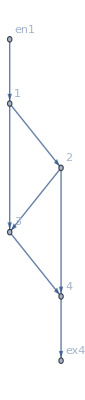

```mathematica
d2e["FG"]
```

```mathematica
(rule=CriticalCongestionSolver[d2e=Data2Equations[Data/.{I1->800,U1->15, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1, S7->1,S8->2,S9->1,S10->1,S11->1,S12->2,S13->1,S14->1,S15->2,S16->1}]])//AbsoluteTiming
```

Iterative boolean convert took 11.5959 seconds to terminate

Iterative boolean convert took 0.447141 seconds to terminate

Iterative boolean convert took 0.40841 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

MFGSS: Multiple solutions: 415≤u5≤416

Picked one value for the variable(s) {u5} {14119/34} (respectively)

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1, S7->1,S8->2,S9->1,S10->1,S11->1,S12->2,S13->1,S14->1,S15->2,S16->1}];//Timing
```

DataToEquations: Triangle inequalities for switching costs: {True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 9.45231 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j418==40&&j419==40&&j420==0&&j421==40&&j422==40&&j425==0&&j427==0&&jt438==0&&jt444==0&&u456==96&&u457==96&&55≤u458≤56&&u459==55&&u460==55&&u462==96
and the rules are:
<|j424→80,u468→15,j423→80,j426→-80+j418+j419-j425,j428→-j418+j420+j421+j425-j427,j429→-80+j418-j420+j422-j425+j427,j430→0,j431→0,jt432→j425,jt433→0,jt434→-80+j418+j419-j425,jt435→0,jt436→80-j419+j425,jt437→j419-j425,jt439→j418-jt438,jt440→j418-j421+j427-jt438,jt441→-j418+j421+jt438,jt442→-j418+j421+j425-j427+jt438,jt443→j420-jt438,jt445→j419-jt444,jt446→j419+j420-j422-jt444,jt447→-j419+j422+jt444,jt448→-80+j418-j420+j422-j425+jt444,jt449→j427-jt444,jt450→-80+j418-j420+j422-j425+j427,jt451→80-j418+j420+j421-j422+j425-j427,jt452→-j418+j420+j421+j425-j427,jt453→j418-j420-j421+j422-j425+j427,jt454→0,jt455→0,u461→15,u463→-j418+j425+u456,u464→-80+j418-j425+u457,u465→-j420+j427+u458,u466→-j418+j420+j425-j427+u459,u467→-80+j418-j420-j425+j427+u460,u469→u462|>

DataToEquations: Mixed system:

DataToEquations: Possible multiple solutions 
{55≤u458≤56,<|j424→80,u468→15,j423→80,j426→-80+40+40-0,j428→-40+0+40+0-0,j429→-80+40-0+40-0+0,j430→0,j431→0,jt432→0,jt433→0,jt434→-80+40+40-0,jt435→0,jt436→80-40+0,jt437→40-0,jt439→40-0,jt440→40-40+0-0,jt441→-40+40+0,jt442→-40+40+0-0+0,jt443→0-0,jt445→40-0,jt446→40+0-40-0,jt447→-40+40+0,jt448→-80+40-0+40-0+0,jt449→0-0,jt450→-80+40-0+40-0+0,jt451→80-40+0+40-40+0-0,jt452→-40+0+40+0-0,jt453→40-0-40+40-0+0,jt454→0,jt455→0,u461→15,u463→-40+0+96,u464→-80+40-0+96,u465→-0+0+u458,u466→-40+0+0-0+55,u467→-80+40-0-0+0+55,u469→96,j418→40,j419→40,j420→0,j421→40,j422→40,j425→0,j427→0,jt438→0,jt444→0,u456→96,u457→96,u459→55,u460→55,u462→96|>}

DataToEquations: There are multiple solutions for the given data.

DataToEquations: Done.

{11.0062,Null}

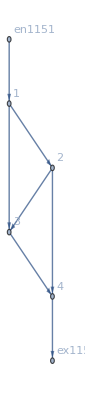

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j418→40,j419→40,j420→0,j421→40,j422→40,j423→80,j424→80,j425→0,j426→0,j427→0,j428→0,j429→0,j430→0,j431→0,jt432→0,jt433→0,jt434→0,jt435→0,jt436→40,jt437→40,jt438→0,jt439→40,jt440→0,jt441→0,jt442→0,jt443→0,jt444→0,jt445→40,jt446→0,jt447→0,jt448→0,jt449→0,jt450→0,jt451→40,jt452→0,jt453→40,jt454→0,jt455→0,u456→96,u457→96,u459→55,u460→55,u461→15,u462→96,u463→56,u464→56,u465→u458,u466→15,u467→15,u468→15,u469→96|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

$Aborted

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

$Aborted

```mathematica
(*alpha[edge_]:= 0.3;*)
(nn=NonLinear[crit];)//AbsoluteTiming
```

Iterative boolean convert took 0.358857 seconds to terminate

Iterative boolean convert took 0.024365 seconds to terminate

Iterative boolean convert took 0.020024 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 1.×10^9

Iterative boolean convert took 0.279225 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

Max error for non-linear solution: 5.×10^8

Iterative boolean convert took 0.297183 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 5.×10^8

Iterative boolean convert took 0.280035 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 5.×10^8

Iterative boolean convert took 0.297716 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 5.×10^8

Iterative boolean convert took 0.268051 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 5.×10^8

Iterative boolean convert took 0.278195 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 5.×10^8

Iterative boolean convert took 0.261056 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 5.×10^8

Iterative boolean convert took 0.247607 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

Max error for non-linear solution: 5.×10^8

Iterative boolean convert took 0.467349 seconds to terminate

Iterative boolean convert took 0.000033 seconds to terminate

Max error for non-linear solution: 5.×10^8

Iterative boolean convert took 0.260563 seconds to terminate

Iterative boolean convert took 0.00001 seconds to terminate

Max error for non-linear solution: 5.×10^8

Iterative boolean convert took 0.267929 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 5.×10^8

Iterative boolean convert took 0.400633 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 5.×10^8

Iterative boolean convert took 0.286642 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 5.×10^8

Iterative boolean convert took 0.283752 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 5.×10^8

Iterated 15 times out of 15

{8.89589,Null}

```mathematica
IsNonLinearSolution[nn][nn["AssoNonCritical"]]
```

All restrictions are True

Nrhs: {-3.5×10^9,3.5×10^9,-8.×10^9,3.5×10^9,-3.5×10^9}
{-j1+j2-If[-j1+j2≠0,45,0],-j3+j4-If[-j3+j4≠0,100/Abs[-j3+j4],0],-j5+j6-If[-j5+j6≠0,1000000000,0],-j7+j8-If[-j7+j8≠0,100/Abs[-j7+j8],0],j10-j9-If[j10-j9≠0,45,0]}

Nlhs: {-3.25×10^9,3.25×10^9,-7.5×10^9,3.25×10^9,-3.25×10^9}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9}

Max error for non-linear solution: 5.×10^8

<|u1→45.,u2→2.5×10^8,u3→45.,u4→-2.5×10^8,u5→2.5×10^8,u6→-2.5×10^8,u7→2.5×10^8,u8→0.,u9→-2.5×10^8,u10→0.,u11→0.,u12→0.,u13→45.,u14→45.,j1→3.5×10^9,j2→0.,j3→0.,j4→3.5×10^9,j5→7.×10^9,j6→0.,j7→0.,j8→3.5×10^9,j9→3.5×10^9,j10→0.,j11→0.,j12→4000.,j13→0.,j14→4000.,jt1→3.5×10^9,jt2→0.,jt3→0.,jt4→0.,jt5→0.,jt6→4000.,jt7→0.,jt8→0.,jt9→3.5×10^9,jt10→3.5×10^9,jt11→0.,jt12→0.,jt13→3.5×10^9,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→3.5×10^9,jt19→3.5×10^9,jt20→4000.,jt21→0.,jt22→0.,jt23→0.,jt24→0.|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```